```mathematica
c =Import["/home/jwb/Documents/Json/longitudinal/Theano-Theano-commits-count.csv"]
```

{{201301,124},{201302,310},{201303,239},{201304,133},{201305,155},{201306,163},{201307,168},{201308,126},{201309,172},{201310,164},{201311,203},{201312,202},{200801,63},{200802,57},{200803,133},{200804,146},{200805,131},{200806,44},{200807,26},{200808,39},{200809,139},{200810,122},{200811,95},{200812,49},{201401,151},{201402,175},{201403,118},{201404,235},{201405,270},{201406,271},{201407,270},{201408,316},{201409,227},{201410,361},{201411,304},{201412,187},{200901,31},{200902,144},{200903,362},{200904,63},{200905,60},{200906,120},{200907,76},{200908,135},{200909,142},{200910,176},{200911,83},{200912,64},{201501,258},{201502,229},{201503,415},{201504,401},{201505,498},{201506,425},{201507,625},{201508,410},{201509,414},{201510,351},{201511,208},{201512,215},{201001,470},{201002,330},{201003,267},{201004,166},{201005,138},{201006,208},{201007,101},{201008,92},{201009,127},{201010,106},{201011,320},{201012,153},{201601,262},{201602,411},{201603,332},{201604,240},{201605,242},{201606,294},{201607,157},{201608,217},{201609,295},{201610,297},{201611,330},{201612,22},{201101,188},{201102,147},{201103,309},{201104,143},{201105,193},{201106,416},{201107,521},{201108,146},{201109,175},{201110,330},{201111,285},{201112,292},{201201,407},{201202,378},{201203,354},{201204,176},{201205,138},{201206,247},{201207,275},{201208,434},{201209,475},{201210,308},{201211,310},{201212,171}}

```mathematica
dateify[l_]:=Sort@Table[{DateString[DateObject[ToExpression/@StringPartition[ToString[l[[n]][[1]]],UpTo[4]]],{"Year","-","Month"}],l[[n]][[2]]},{n,Length@l}]
```

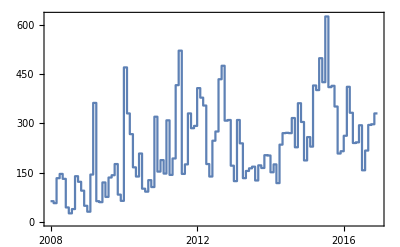

```mathematica
DateListStepPlot[dateify[c]]
```

```mathematica
SetDirectory["/home/jwb/Documents/Json/longitudinal/"];
files=Import[#]&/@FileNames["*.csv"];
```

```mathematica
mlLabels={"Caffe","CNTK","DL4J","TensorFlow","Theano","Torch7"};
```

```mathematica
Export["/home/jwb/Documents/Json/longitudinal/longplot.png",DateListPlot[dateify/@files,ImageSize->{1600,1000},PlotRange->Full,PlotLegends->mlLabels,PlotStyle->Thick,LabelStyle->Large,FrameLabel->{"Time","Commits Per Month"}]]
```

/home/jwb/Documents/Json/longitudinal/longplot.png

```mathematica
a=dateify/@files;
```

```mathematica
Table[Export["/home/jwb/Documents/Json/longitudinal/Clean/"<>mlLabels[[n]]<>".csv",Transpose@a[[n]]],{n,6}]
```

{/home/jwb/Documents/Json/longitudinal/Clean/Caffe.csv,/home/jwb/Documents/Json/longitudinal/Clean/CNTK.csv,/home/jwb/Documents/Json/longitudinal/Clean/DL4J.csv,/home/jwb/Documents/Json/longitudinal/Clean/TensorFlow.csv,/home/jwb/Documents/Json/longitudinal/Clean/Theano.csv,/home/jwb/Documents/Json/longitudinal/Clean/Torch7.csv}

```mathematica
"/home/jwb/Documents/Json/longitudinal/Clean/"<>"Hi"
```

/home/jwb/Documents/Json/longitudinal/Clean/Hi

```mathematica
mlLabels[1]
```

{Caffe,CNTK,DL4J,TensorFlow,Theano,Torch7}[1]

```mathematica
a
```

{{{2013-09,131},{2013-10,110},{2013-11,72},{2013-12,26},{2014-01,59},{2014-02,252},{2014-03,288},{2014-04,197},{2014-05,153},{2014-06,164},{2014-07,264},{2014-08,282},{2014-09,299},{2014-10,161},{2014-11,54},{2014-12,71},{2015-01,118},{2015-02,122},{2015-03,93},{2015-04,35},{2015-05,104},{2015-06,37},{2015-07,49},{2015-08,111},{2015-09,84},{2015-10,66},{2015-11,68},{2015-12,28},{2016-01,47},{2016-02,43},{2016-03,29},{2016-04,38},{2016-05,48},{2016-06,18},{2016-07,23},{2016-08,26},{2016-09,16},{2016-10,9},{2016-11,27},{2016-12,2}},{{2014-07,1},{2014-08,2},{2014-09,60},{2014-10,96},{2014-11,111},{2014-12,19},{2015-01,54},{2015-02,119},{2015-03,63},{2015-04,111},{2015-05,152},{2015-06,110},{2015-07,285},{2015-08,293},{2015-09,359},{2015-10,418},{2015-11,420},{2015-12,534},{2016-01,348},{2016-02,399},{2016-03,831},{2016-04,1136},{2016-05,640},{2016-06,457},{2016-07,335},{2016-08,539},{2016-09,744},{2016-10,1179},{2016-11,578},{2016-12,59}},{{2013-11,2},{2013-12,76},{2014-01,63},{2014-02,75},{2014-03,197},{2014-04,156},{2014-05,95},{2014-06,71},{2014-07,67},{2014-08,156},{2014-09,172},{2014-10,99},{2014-11,124},{2014-12,122},{2015-01,185},{2015-02,70},{2015-03,83},{2015-04,81},{2015-05,174},{2015-06,215},{2015-07,446},{2015-08,409},{2015-09,220},{2015-10,112},{2015-11,154},{2015-12,211},{2016-01,283},{2016-02,155},{2016-03,170},{2016-04,123},{2016-05,159},{2016-06,222},{2016-07,277},{2016-08,178},{2016-09,255},{2016-10,273},{2016-11,345},{2016-12,15}},{{2015-11,100},{2015-12,429},{2016-01,714},{2016-02,886},{2016-03,964},{2016-04,654},{2016-05,829},{2016-06,1010},{2016-07,783},{2016-08,1059},{2016-09,1185},{2016-10,1489},{2016-11,1266},{2016-12,49}},{{2008-01,63},{2008-02,57},{2008-03,133},{2008-04,146},{2008-05,131},{2008-06,44},{2008-07,26},{2008-08,39},{2008-09,139},{2008-10,122},{2008-11,95},{2008-12,49},{2009-01,31},{2009-02,144},{2009-03,362},{2009-04,63},{2009-05,60},{2009-06,120},{2009-07,76},{2009-08,135},{2009-09,142},{2009-10,176},{2009-11,83},{2009-12,64},{2010-01,470},{2010-02,330},{2010-03,267},{2010-04,166},{2010-05,138},{2010-06,208},{2010-07,101},{2010-08,92},{2010-09,127},{2010-10,106},{2010-11,320},{2010-12,153},{2011-01,188},{2011-02,147},{2011-03,309},{2011-04,143},{2011-05,193},{2011-06,416},{2011-07,521},{2011-08,146},{2011-09,175},{2011-10,330},{2011-11,285},{2011-12,292},{2012-01,407},{2012-02,378},{2012-03,354},{2012-04,176},{2012-05,138},{2012-06,247},{2012-07,275},{2012-08,434},{2012-09,475},{2012-10,308},{2012-11,310},{2012-12,171},{2013-01,124},{2013-02,310},{2013-03,239},{2013-04,133},{2013-05,155},{2013-06,163},{2013-07,168},{2013-08,126},{2013-09,172},{2013-10,164},{2013-11,203},{2013-12,202},{2014-01,151},{2014-02,175},{2014-03,118},{2014-04,235},{2014-05,270},{2014-06,271},{2014-07,270},{2014-08,316},{2014-09,227},{2014-10,361},{2014-11,304},{2014-12,187},{2015-01,258},{2015-02,229},{2015-03,415},{2015-04,401},{2015-05,498},{2015-06,425},{2015-07,625},{2015-08,410},{2015-09,414},{2015-10,351},{2015-11,208},{2015-12,215},{2016-01,262},{2016-02,411},{2016-03,332},{2016-04,240},{2016-05,242},{2016-06,294},{2016-07,157},{2016-08,217},{2016-09,295},{2016-10,297},{2016-11,330},{2016-12,22}},{{2012-01,4},{2012-02,41},{2012-03,15},{2012-04,5},{2012-05,6},{2012-06,3},{2012-07,5},{2012-08,16},{2012-09,13},{2012-10,3},{2012-11,3},{2012-12,17},{2013-01,4},{2013-02,10},{2013-03,4},{2013-04,8},{2013-05,3},{2013-06,6},{2013-07,7},{2013-08,4},{2013-09,2},{2013-10,36},{2013-11,3},{2013-12,1},{2014-01,2},{2014-02,21},{2014-03,38},{2014-04,36},{2014-05,16},{2014-06,40},{2014-07,14},{2014-08,5},{2014-09,6},{2014-10,18},{2014-11,30},{2014-12,5},{2015-01,35},{2015-02,24},{2015-03,25},{2015-04,49},{2015-05,32},{2015-06,22},{2015-07,44},{2015-08,25},{2015-09,26},{2015-10,57},{2015-11,47},{2015-12,21},{2016-01,16},{2016-02,52},{2016-03,46},{2016-04,30},{2016-05,14},{2016-06,5},{2016-07,9},{2016-08,21},{2016-09,21},{2016-10,23},{2016-11,14}}}